# Slepton-side γ-radiation

## Load FeynCalc

```mathematica
description="Photon radiation correction to slepton pair production.";
If[$FrontEnd===Null,
$FeynCalcStartupMessages=False;
Print[description];
];
If[$Notebooks===False,
$FeynCalcStartupMessages=False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Calculate the squared amplitude

### Draw diagrams

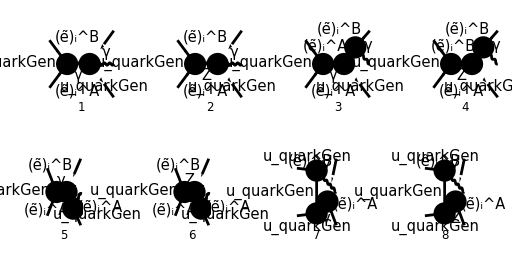

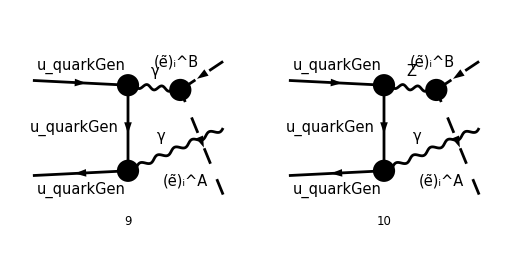

```mathematica
diags=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4]}
];
Paint[
diags,
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[p3, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(3\)]\)"; 
MakeBoxes[p4, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(4\)]\)";
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{p3,k,p4},
ChangeDimension->4,
UndoChiralSplittings->True,
List->False,
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

-(4 (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(γ̄·(k̄-OverBar[p_2])).(γ̄·(OverBar[p_4]-OverBar[p_3])).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (OverBar[p_2]-k̄)^2 (OverBar[p_3]+OverBar[p_4])^2)-(4 (φ(-OverBar[p_2])).(γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄·(-OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2 (OverBar[p_3]+OverBar[p_4])^2)-(4 (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) IndexDelta(A,B) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2)-(2 (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])) IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_3]·(ε̄)^*(k))) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2 ((-k̄-OverBar[p_3])^2-(MSf(A,2,i))^2))-(2 (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1])) IndexDelta(A,B) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) e^3 δ_Col1Col2)/(3 (k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))+(ⅈ (φ(-OverBar[p_2])).(γ̄·(ε̄)^*(k)).(γ̄·(k̄-OverBar[p_2])).((2 ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) e^2 δ_Col1Col2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (OverBar[p_2]-k̄)^2 ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))+(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(OverBar[p_4]-OverBar[p_3])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(γ̄·(-OverBar[p_2]+OverBar[p_3]+OverBar[p_4])).(γ̄·(ε̄)^*(k)).(φ(OverBar[p_1])) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (OverBar[p_2]-OverBar[p_3]-OverBar[p_4])^2 ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))+(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(ε̄)^*(k)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(ε̄)^*(k)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))+(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(k̄+OverBar[p_3]-OverBar[p_4])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_3]·(ε̄)^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k̄-OverBar[p_3])^2-(MSf(B,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))+(ⅈ (φ(-OverBar[p_2])).((2 ⅈ (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])) (-(k̄·(ε̄)^*(k))-2 (OverBar[p_4]·(ε̄)^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2) ((k̄+OverBar[p_3]+OverBar[p_4])^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))

### Extract the fifth diagram, and change 2/3 to e_Q

```mathematica
Pair[Momentum[k],Momentum[Polarization[k,-I]]]=0; (*Lorenz gauge*)
M5[0]=Part[M[0],5];
M5[1]=M5[0] 3/2 SMP["e_Q"]
```

(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (OverBar[p_4]·(ε̄)^*(k)) (φ(-OverBar[p_2])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(OverBar[p_1])))/((k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))

```mathematica
M5[1]//DiracSimplify
```

(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (OverBar[p_4]·(ε̄)^*(k)) (φ(-OverBar[p_2])).(γ̄·(k̄+OverBar[p_4])).(φ(OverBar[p_1])))/((k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))-(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (OverBar[p_4]·(ε̄)^*(k)) (φ(-OverBar[p_2])).(γ̄·OverBar[p_3]).(φ(OverBar[p_1])))/((k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))

```mathematica
M5CC[1]=ComplexConjugate[M5[1]]
```

(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (OverBar[p_4]·ε̄(k)) (φ(OverBar[p_1])).(γ̄·(k̄-OverBar[p_3]+OverBar[p_4])).(φ(-OverBar[p_2])))/((k̄+OverBar[p_3]+OverBar[p_4])^2 ((k̄+OverBar[p_4])^2-(MSf(A,2,i))^2))

```mathematica
FCClearScalarProducts[];
(*SetMandelstam*) (*How do I do this for a 2->3 process?*)
```

```mathematica
SP[p1,p1]=0;SP[p2,p2]=0;SP[k,k]=0;
M5Squared[0]=(M5[1] M5CC[1])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//DoPolarizationSums[#,k,0]&//DiracSimplify//SUNSimplify[#,SUNNToCACF->False]&//Simplify
```

(4 e^6 OverBar[p_4]^2 e_Q^2 IndexDelta(A,B) (-2 (k̄·OverBar[p_1]) (k̄·OverBar[p_2]-OverBar[p_2]·OverBar[p_3]+OverBar[p_2]·OverBar[p_4])-2 (k̄·OverBar[p_3]) (OverBar[p_1]·OverBar[p_2])+2 (k̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_3])+2 (k̄·OverBar[p_4]) (OverBar[p_1]·OverBar[p_2])-2 (k̄·OverBar[p_2]) (OverBar[p_1]·OverBar[p_4])-2 (OverBar[p_1]·OverBar[p_2]) (OverBar[p_3]·OverBar[p_4])+2 (OverBar[p_1]·OverBar[p_4]) (OverBar[p_2]·OverBar[p_3])+2 (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_4])+OverBar[p_3]^2 (OverBar[p_1]·OverBar[p_2])-2 (OverBar[p_1]·OverBar[p_3]) (OverBar[p_2]·OverBar[p_3])+OverBar[p_4]^2 (OverBar[p_1]·OverBar[p_2])-2 (OverBar[p_1]·OverBar[p_4]) (OverBar[p_2]·OverBar[p_4])))/(N (2 (k̄·OverBar[p_3])+2 (k̄·OverBar[p_4])+2 (OverBar[p_3]·OverBar[p_4])+OverBar[p_3]^2+OverBar[p_4]^2)^2 (2 (k̄·OverBar[p_4])+OverBar[p_4]^2-(MSf(A,2,i))^2)^2)